```mathematica
Needs["ErrorBarPlots`"]
```

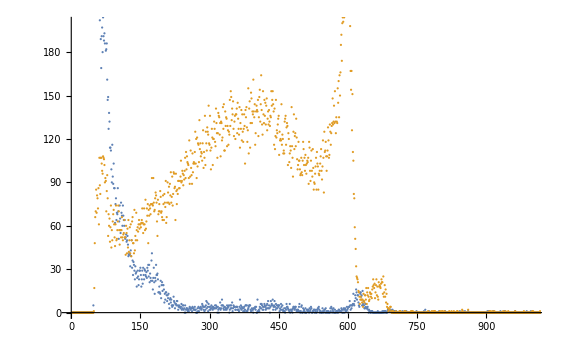

```mathematica
imp=Import[NotebookDirectory[]<>"../data/part3/Co-Si.mca","Table"];
data=Flatten[Drop[Drop[imp,12],-1]];
data=Table[{i,data[[i]]},{i,1,Length[data]}];
imp2=Import[NotebookDirectory[]<>"../data/part3/Co-CdTe.mca","Table"];
data2=Flatten[Drop[Drop[imp2,12],-1]];
ListPlot[{data,data2},PlotRange->{{0,1000},{0,200}}]
```

42

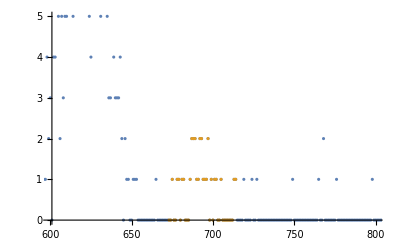

```mathematica
start=672;
end=714;
datacut=Drop[Drop[data,start],-(Length[data]-end)];
Length[datacut]
ListPlot[{data,datacut},PlotRange->{{600,800},{0,5}}]
```

{1,2,2,5,6,5,3,2,1,0}

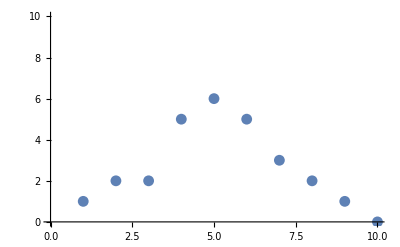

```mathematica
datacutsum=Table[Sum[datacut[[bin i-n,2]],{n,0,bin-1}],{i,1,Floor[Length[datacut]/bin]}]
ListPlot[datacutsum,PlotRange->{{0,Length[datacutsum]},{0,10}}]
```

```mathematica
m[x_]:=Sum[x[[i,2]]/x[[i,3]]^2,{i,1,Length[x]}]
v[x_]:=1/Sum[1/x[[i,3]]^2,{i,1,Length[x]}]
avmean[x_]:=m[x]*v[x];
```

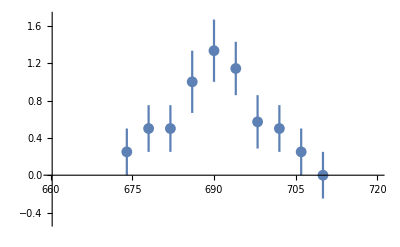

{{674,1/4,1/4},{678,1/2,1/4},{682,1/2,1/4},{686,1,1/3},{690,4/3,1/3},{694,8/7,2/7},{698,4/7,2/7},{702,1/2,1/4},{706,1/4,1/4},{710,0,1/4}}

```mathematica
bin=4;
errdatacutsum={};
errdatacutt=errdatacut;
For[i=1,i≤Floor[Length[datacut]/bin],i++,{errdatacutsum=Append[errdatacutsum,{start+i bin -bin/2,avmean[Take[errdatacutt,bin]],v[Take[errdatacutt,bin]]}],
errdatacutt=Drop[errdatacutt,bin]}
]

ErrorListPlot[
Table[
{{errdatacutsum[[i,1]],errdatacutsum[[i,2]]},ErrorBar[errdatacutsum[[i,3]]]},{i,1,Length[errdatacutsum]}
]
,PlotRange->{{660,720},{-0.5,1.7}}
]

errdatacutsum
```

```mathematica
Export[NotebookDirectory[]<>"../data/part3/Co-Si_mergedbins.txt",errdatacutsum//N,"Table"]
```

/home/moritz/FP1/1002-Halbleiter/src/../data/part3/Co-Si_mergedbins.txt